# Юрьев В. А. Лабораторная работа №2: Символьные вычисления. Строки и текст

## 1.1 Придумайте и определите символьное выражение, содержащее не менее трех слагаемых, причем хотя бы одно из них должно быть рациональным выражением.

Раскрывает произведения и положительные целые степени в выражении

```mathematica
t1 =  (9(x^3+ 15)(x^2-y^2))/((5 x^2-1)(x-y))+6(x+y)^3+x^3+y^3
Expand[t1]
```

x^3+y^3+6 (x+y)^3+(9 (15+x^3) (x^2-y^2))/((-1+5 x^2) (x-y))

7 x^3+(135 x^2)/((-1+5 x^2) (x-y))+(9 x^5)/((-1+5 x^2) (x-y))+18 x^2 y+18 x y^2-(135 y^2)/((-1+5 x^2) (x-y))-(9 x^3 y^2)/((-1+5 x^2) (x-y))+7 y^3

Раскрывает все произведения и целые степени в любой части.

```mathematica
ExpandAll[t1]
```

```mathematica
7 x^3+18 x^2 y+18 x y^2+7 y^3+(135 x^2)/(-x+5 x^3+y-5 x^2 y)+(9 x^5)/(-x+5 x^3+y-5 x^2 y)-(135 y^2)/(-x+5 x^3+y-5 x^2 y)-(9 x^3 y^2)/(-x+5 x^3+y-5 x^2 y)
```

Множит многочлен по целым числам

```mathematica
Factor[t1]
1/(-1+5 x^2)(x+y) (135-7 x^2+9 x^3+35 x^4-11 x y+55 x^3 y-7 y^2+35 x^2 y^2)
```

Складывает члены в сумме с общим знаменателем и исключает множители в результате

```mathematica
Together[t1]
```

(135 x-7 x^3+9 x^4+35 x^5+135 y-18 x^2 y+9 x^3 y+90 x^4 y-18 x y^2+90 x^3 y^2-7 y^3+35 x^2 y^3)/(-1+5 x^2)

Переписывает рациональное выражение как сумму членов с минимальными знаменателями.

```mathematica
Apart[t1]
(x (135-7 x^2+9 x^3+35 x^4))/(-1+5 x^2)+(9 (15-2 x^2+x^3+10 x^4) y)/(-1+5 x^2)+18 x y^2+7 y^3
```

Избавляется от общих множителей в числителе и знаменателе выражения.

```mathematica
Cancel[t1]
x^3+y^3+(9 (15+x^3) (x+y))/(-1+5 x^2)+6 (x+y)^3
```

Выполняет последовательность алгебраических и других преобразований и возвращает простейшую форму, которую находит.

```mathematica
Simplify[t1]
x^3+y^3+(9 (15+x^3) (x+y))/(-1+5 x^2)+6 (x+y)^3
```

```mathematica
Simplify[t1] // TraditionalForm
x^3+(9 (x^3+15) (x+y))/(5 x^2-1)+6 (x+y)^3+y^3
```

## 1.2 Приведите выражение t1 к общему знаменателю и с помощью функции Numerator определите числитель полученного выражения, обозначив его t2. С помощью функции Collect представьте выражение t2 в виде полинома по степеням х или у . Определите максимальную степень n одной из переменных, например, х в выражении t2и коэффициент при хn. Используйте Exponent и Coefficient.

```mathematica
t2=Numerator[Together[t1]];t2
135 x-7 x^3+9 x^4+35 x^5+135 y-18 x^2 y+9 x^3 y+90 x^4 y-18 x y^2+90 x^3 y^2-7 y^3+35 x^2 y^3
```

Группируем по Х или У

```mathematica
Collect[t2,x]
35 x^5+135 y-7 y^3+x^4 (9+90 y)+x (135-18 y^2)+x^3 (-7+9 y+90 y^2)+x^2 (-18 y+35 y^3)
```

```mathematica
Collect[t2,y]
135 x-7 x^3+9 x^4+35 x^5+(135-18 x^2+9 x^3+90 x^4) y+(-18 x+90 x^3) y^2+(-7+35 x^2) y^3
```

Выдает максимальную степень, с которой искомая появляется в развернутой форме.

```mathematica
Exponent[t2,y]
3
```

Возвращает коэффициент искомой в N степени, поэтому 3 параметра передаем.

```mathematica
Coefficient[t2,y,3]
-7+35 x^2
```

## 2.1 С помощью функции D вычислить производную функции.

Найдем частную производную

```mathematica
D[x^n Cos[x],x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

## 2.2 Вычислить производные

```mathematica
D[(a*x^3+2 x^2),x]
```

4 x+3 a x^2

```mathematica
D[(4 x^2-5x+8-3/x),{x,3}]
```

18/x^4

```mathematica
D[(x^3* y^2+3 x^2),{x,3},{y,2}]
```

```mathematica
12
```

## 2.3 Используя функцию Integrate вычислить интеграл

```mathematica
Integrate[ 1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

## 2.4 Вычислить интегралы, затем продифференцировать полученные выражения и убедиться, что получаемые результаты совпадают ? подынтегральными выражениями.

```mathematica
Integrate[x^3/(x^2+1),x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Together[D[x^2/2-1/2 Log[1+x^2],x]]
```

x^3/(1+x^2)

```mathematica
Integrate[1/(x^3+1),x] // Simplify
```

1/6 (2 √3 ArcTan[(-1+2 x)/(√3)]+2 Log[1+x]-Log[1-x+x^2])

```mathematica
ExpandAll[Together[D[%,x]]]
```

1/(1+x^3)

## 2.5 Вычислить определенный интеграл

```mathematica
∫_1^4 (5x-2 √x+32/x^3)ⅆx
```

259/6

## 2.6 Вычислить интегралы

```mathematica
∫_0^1 (1+x^4)^(1/3)ⅆx
Hypergeometric2F1[-1/3,1/4,5/4,-1]
```

```mathematica
∫_0^1. (1+x^4)^(1/3)ⅆx
```

1.05753

## 3.1 Используя функцию Solve решить уравнение

```mathematica
Solve[a*x^4+x^2+3==0,x]
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

## 3.2 Найти точное решение системы уравнений

```mathematica
Solve[x^2+y==1 && y^2-x^2==2,{x,y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

## 3.3 Решить систему уравнений

```mathematica
NSolve[x^2-y^2==1 && y^3+x==5,{x,y}]
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

## 3.4 Найти общие решения дифференциальных уравнений,используя функцию DSOLVE

Решает дифференциальное уравнение для функции с независимой переменной x.

```mathematica
task1 =DSolve[{y'[x]-y[x]Tan[x]==x,y[0]==0},y[x], x]
```

{{y[x]→1-Sec[x]+x Tan[x]}}

```mathematica
task1[[1,1,2]]
```

1-Sec[x]+x Tan[x]

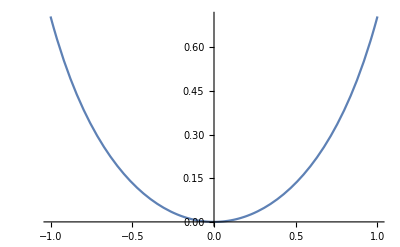

```mathematica
Plot[task1[[1,1,2]], {x, -1, 1}]
```

```mathematica
task2 =DSolve[{y'[x]+y[x]Tan[x]==1/Cos[x],y[0]==0},y[x],x]
```

{{y[x]→Sin[x]}}

```mathematica
task2[[1,1,2]]
```

Sin[x]

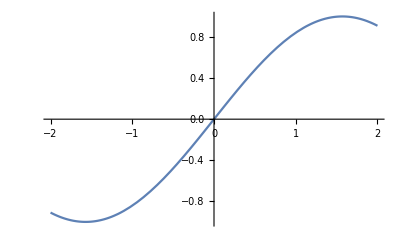

```mathematica
Plot[task2[[1,1,2]],{x,-2,2}]
```

## 3.5 Самостоятельно выбрав граничные условия найти решение дифференциального уравнения в символьном виде.

```mathematica
task3 = DSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==1, y'[0]==1}, y[x], x] // FullSimplify
```

{{y[x]→1/2 ⅇ^(x/2) π (-((AiryAi[1/4]+2 AiryAiPrime[1/4]) AiryBi[1/4-x])+AiryAi[1/4-x] (AiryBi[1/4]+2 AiryBiPrime[1/4]))}}

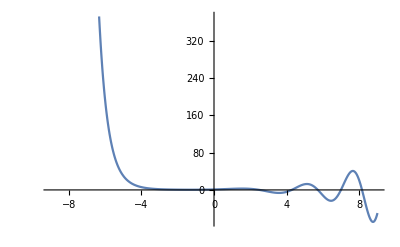

```mathematica
anotherTask = Plot[task3[[1,1,2]],{x,-9,9}]
```

```mathematica
task4 = NDSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==1, y'[0]==1}, y[x], {x, -9,9}]
{{y[x]->InterpolatingFunction[…][x]}}
```

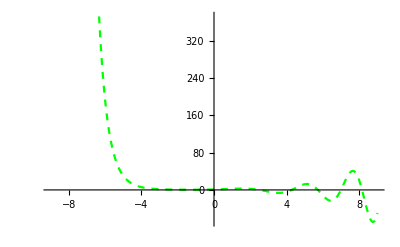

```mathematica
oneMoreTask = Plot[task4[[1,1,2]], {x, -9, 9},PlotStyle->{Dashed, Green}]
```

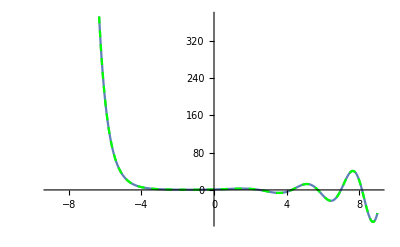

```mathematica
finalTask = Show[anotherTask, oneMoreTask]
```